This guy needs to illustrate simple graph, multiedges, loops, directed vs undirected, weighted, degree (+ in and outdegree), neighbors, incident, predecessory, successor

```mathematica
p = Graph[{1,2,3,4,5,6,7,8},{1<->3,2<->4,5<->7,4<->7,3<->6,3<->2, 3<->8,2<->5,1<->5,6<->8,6<->5,4<->8},
VertexSize->0.2,EdgeStyle->{1<->3->Red,3<->2->Red,2<->4->Red},VertexStyle->{1->Red,2->Red,3->Red,4->Red}]
```

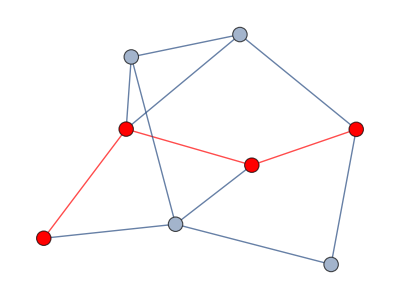

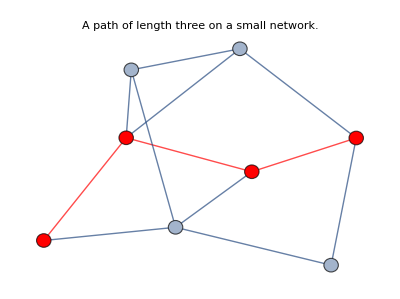

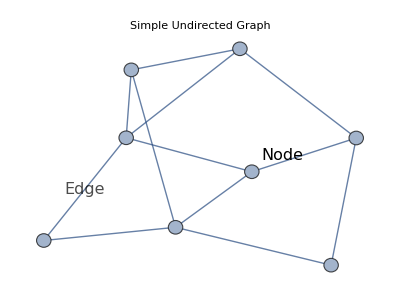

```mathematica
g1 = Graph[{1,2,3,4,5,6,7,8},{1<->3,2<->4,5<->7,4<->7,3<->6,3<->2, 3<->8,2<->5,1<->5,6<->8,6<->5,4<->8},
VertexSize->0.2,
VertexLabels->{2->"Node"},EdgeLabels->{1<->3->"Edge"},
VertexLabelStyle->Directive[16,Black,FontFamily->"Helvetica"],
EdgeLabelStyle->Directive[16,Black,FontFamily->"Helvetica"],PlotLabel->Style[Framed[Style["Simple Undirected Graph",16],FrameMargins->Large,FrameStyle->Directive[Black,Thickness[0.2]]],Black,FontFamily->"Helvetica"]]
```

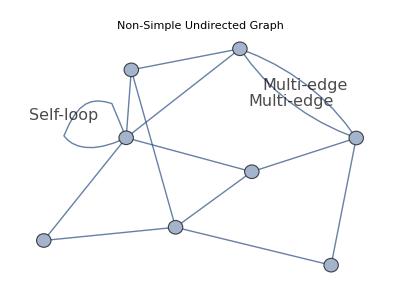

```mathematica
g2 =Graph[{1,2,3,4,
5,6,7,8},{1<->3,2<->4,5<->7,4<->7,3<->6,3<->2, 3<->8,2<->5,1<->5,6<->8,6<->5,4<->8, 4<->8,3<->3},EdgeLabels->{4<->8->"Multi-edge", 3<->3 ->"Self-loop"},
VertexSize->0.2,
VertexLabelStyle->Directive[16,Black,FontFamily->"Helvetica"],
EdgeLabelStyle->Directive[16,Black,FontFamily->"Helvetica"],PlotLabel->Style[Framed[Style["Non-Simple Undirected Graph",16],FrameMargins->Large,FrameStyle->Directive[Black,Thickness[0.2]]],Black,FontFamily->"Helvetica"]]
```

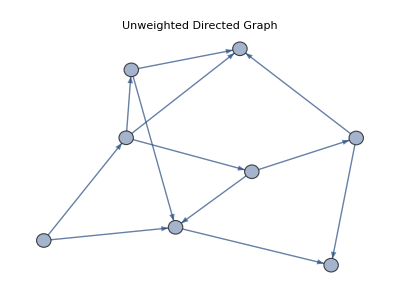

```mathematica
g3 = Graph[{1,2,3,4,5,6,7,8},{1->3,2->4,5->7,4->7,3->6,3->2, 3->8,2->5,1->5,6->8,6->5,4->8},
VertexSize->0.2,
GraphLayout->"SpringElectricalEmbedding",VertexLabelStyle->Directive[16,Black,FontFamily->"Helvetica"],
EdgeLabelStyle->Directive[16,Black,FontFamily->"Helvetica"],PlotLabel->Style[Framed[Style["Unweighted Directed Graph",16],FrameMargins->Large,FrameStyle->Directive[Black,Thickness[0.2]]],Black,FontFamily->"Helvetica"]]
```

```mathematica
EdgeCount[g3]
```

12

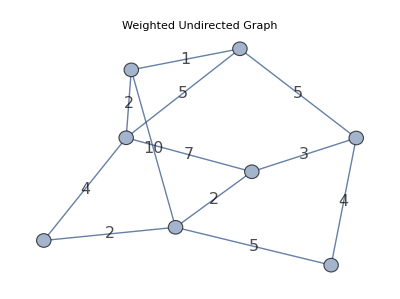

```mathematica
g4 = Graph[{1,2,3,4,5,6,7,8},{1<->3,2<->4,5<->7,4<->7,3<->6,3<->2, 3<->8,2<->5,1<->5,6<->8,6<->5,4<->8},
EdgeWeight->{4,3,5,4,2,7,5,2,2,1,10,5},
VertexSize->0.2,
EdgeLabels->"EdgeWeight",
GraphLayout->"SpringElectricalEmbedding",VertexLabelStyle->Directive[16,Black,FontFamily->"Helvetica"],
EdgeLabelStyle->Directive[16,Black,FontFamily->"Helvetica"],PlotLabel->Style[Framed[Style["Weighted Undirected Graph",16],FrameMargins->Large,FrameStyle->Directive[Black,Thickness[0.2]]],Black,FontFamily->"Helvetica"]]
```

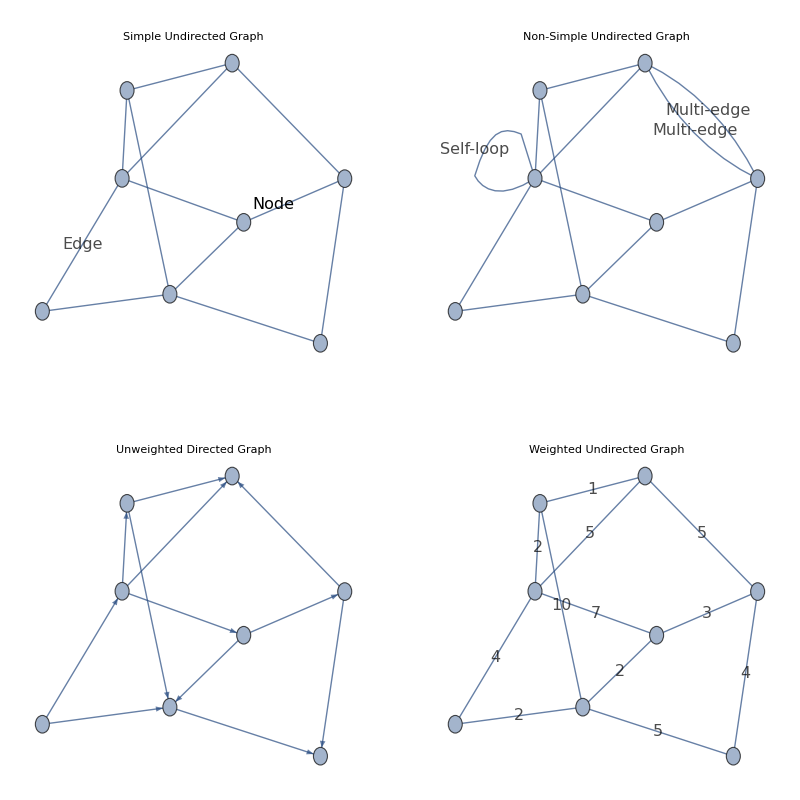

```mathematica
GraphicsGrid[{{g1,g2},{g3,g4}},Frame->All, ImageSize->Full]
```

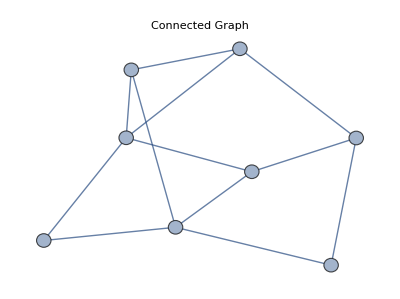

```mathematica
g5 = Graph[{1,2,3,4,5,6,7,8},{1<->3,2<->4,5<->7,4<->7,3<->6,3<->2, 3<->8,2<->5,1<->5,6<->8,6<->5,4<->8},
VertexSize->0.2,VertexLabelStyle->Directive[16,Black,FontFamily->"Helvetica"],
EdgeLabelStyle->Directive[16,Black,FontFamily->"Helvetica"],PlotLabel->Style[Framed[Style["Connected Graph",16],FrameMargins->Large,FrameStyle->Directive[Black,Thickness[0.2]]],Black,FontFamily->"Helvetica"]]
```

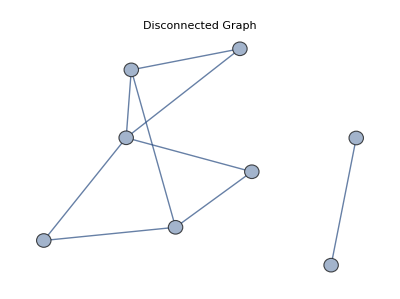

```mathematica
g6 = Graph[{1,2,3,4,5,6,7,8},{1<->3,2<->4,5<->7,4<->7,3<->6,3<->2, 3<->8,2<->5,1<->5,6<->8,6<->5,4<->8},EdgeStyle->{4<->8->White,5<->7->White,2<->4->White},
VertexSize->0.2,VertexLabelStyle->Directive[16,Black,FontFamily->"Helvetica"],
EdgeLabelStyle->Directive[16,Black,FontFamily->"Helvetica"],PlotLabel->Style[Framed[Style["Disconnected Graph",16],FrameMargins->Large,FrameStyle->Directive[Black,Thickness[0.2]]],Black,FontFamily->"Helvetica"]]
```

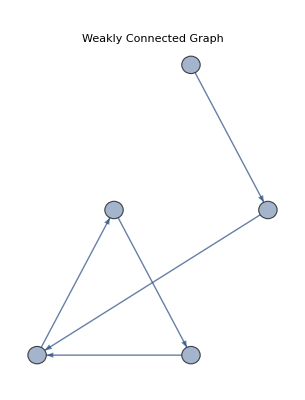

```mathematica
g7= Graph[{1,2,3,4,5},{1->2,2->3,3->4,4->1,4->5,5->3},EdgeStyle->{(4->1)->White},GraphLayout->"LayeredEmbedding",
VertexSize->0.12,VertexLabelStyle->Directive[16,Black,FontFamily->"Helvetica"],
EdgeLabelStyle->Directive[16,Black,FontFamily->"Helvetica"],PlotLabel->Style[Framed[Style["Weakly Connected Graph",16],FrameMargins->Large,FrameStyle->Directive[Black,Thickness[0.2]]],Black,FontFamily->"Helvetica"]]
```

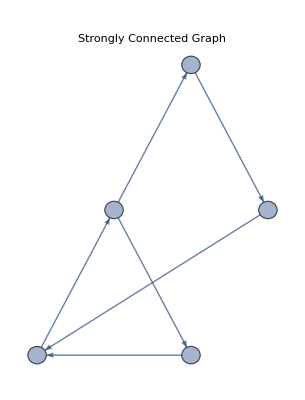

```mathematica
g8 = Graph[{1,2,3,4,5},{1->2,2->3,3->4,4->1,4->5,5->3},GraphLayout->"LayeredEmbedding",
VertexSize->0.12,VertexLabelStyle->Directive[16,Black,FontFamily->"Helvetica"],
EdgeLabelStyle->Directive[16,Black,FontFamily->"Helvetica"],PlotLabel->Style[Framed[Style["Strongly Connected Graph",16],FrameMargins->Large,FrameStyle->Directive[Black,Thickness[0.2]]],Black,FontFamily->"Helvetica"]]
```

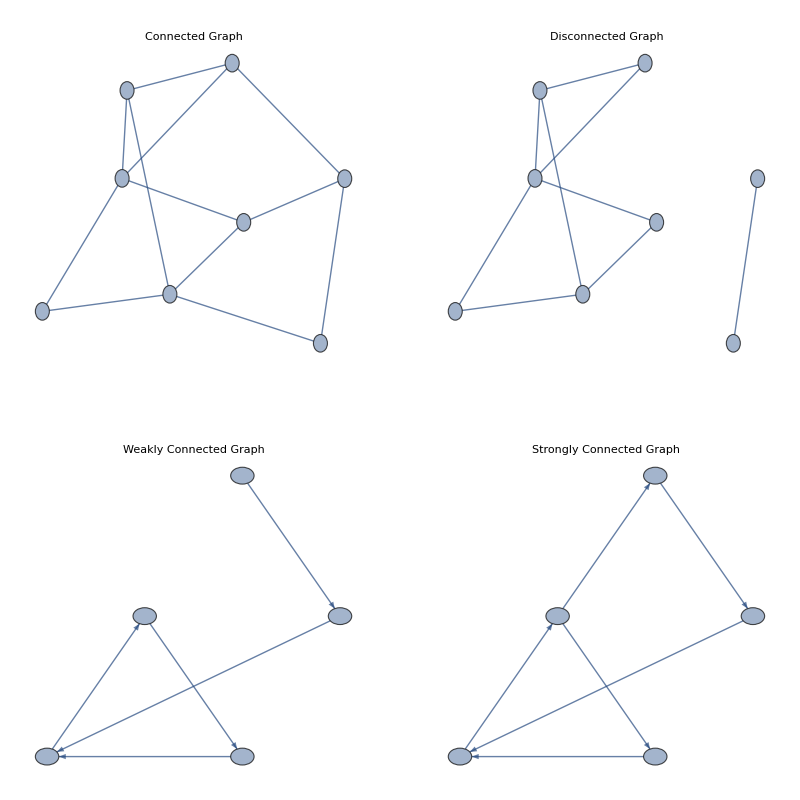

```mathematica
GraphicsGrid[{{g5,g6},{g7,g8}},Frame->All, ImageSize->Full]
```

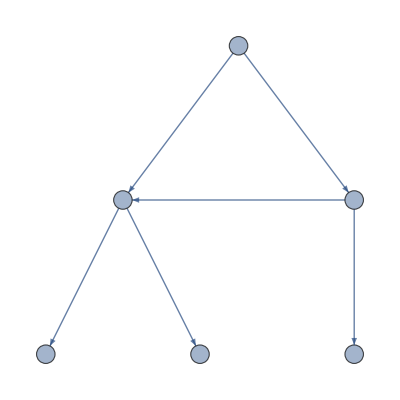

```mathematica
h = Graph[{1,2,3,4,5,7},{2->3,7->2,7->4, 1->7,2->5,1->2},GraphLayout->"LayeredEmbedding",
VertexSize->0.12,VertexLabelStyle->Directive[16,Black,FontFamily->"Helvetica"],
EdgeLabelStyle->Directive[16,Black,FontFamily->"Helvetica"]]
```

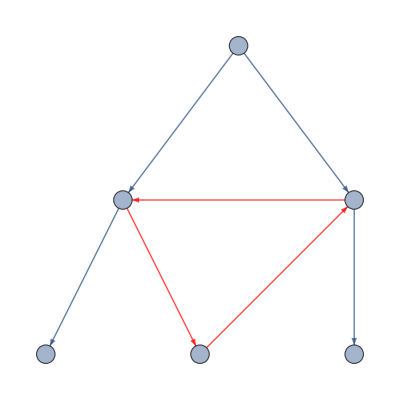

```mathematica
h2 =Graph[{1,2,3,4,5,7},{2->3,7->2,7->4,1->7,2->5,1->2,5->7},GraphLayout->"LayeredEmbedding",EdgeStyle->{(2->5)->Red,(5->7)->Red,(7->2)->Red},
VertexSize->0.12,VertexLabelStyle->Directive[16,Black,FontFamily->"Helvetica"],
EdgeLabelStyle->Directive[16,Black,FontFamily->"Helvetica"]]
```

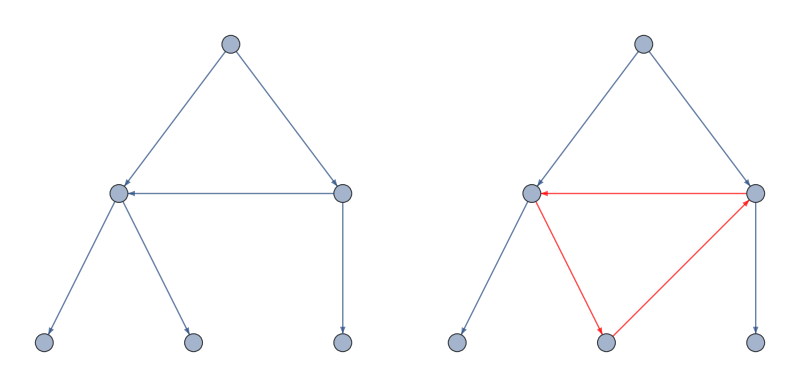

```mathematica
GraphicsGrid[{{h,h2}},ImageSize->Full]
```

```mathematica
ExampleData[{"NetworkGraph","SimpleFoodWeb"}]
```

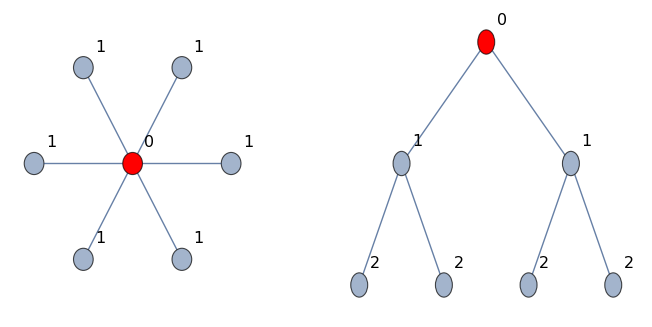

```mathematica
GraphicsGrid[{{Show[Graph[{1,2,3,4,5,6,7},{1<->2,1<->3,1<->4,1<->5,1<->6,1<->7},VertexLabels->{1->0,2->1,3->1,4->1,5->1,6->1,7->1},VertexStyle->{1->Red},GraphLayout->"RadialDrawing",VertexSize->0.2,
VertexLabelStyle->Directive[16,Black,FontFamily->"Helvetica"]],ImageSize->{240,240}],Show[Graph[{1,2,3,4,5},{1<->2,1<->3,2<->4,2<->5,3<->6,3<->7},VertexLabels->{1->0,2->1,3->1,4->2,5->2,6->2,7->2},VertexStyle->{1->Red},VertexSize->0.2,
VertexLabelStyle->Directive[16,Black,FontFamily->"Helvetica"]],ImageSize->{300,300}]}}]
```

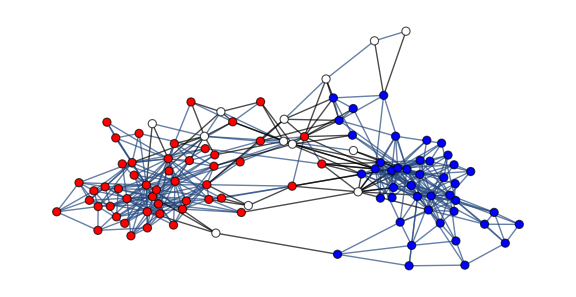

-0.127896

0.723308

```mathematica
test = ExampleData[{"NetworkGraph","USPoliticsBooks"}];
verts = VertexList[test];
For[i=1,i≤VertexCount[test],i++,
v = verts[[i]];
PropertyValue[{test,v},VertexSize]=1.25;
If[PropertyValue[{test,v},"Classification"]=="Conservative",PropertyValue[{test,v},VertexStyle]=Red];
If[PropertyValue[{test,v},"Classification"]=="Liberal",
PropertyValue[{test,v},VertexStyle]=Blue];
If[PropertyValue[{test,v},"Classification"]=="Neutral",
PropertyValue[{test,v},VertexStyle]=White];
]
edges = EdgeList[test];
For[i=1,i≤EdgeCount[test],i++,
s = edges[[i]][[1]];
t = edges[[i]][[2]];
If[PropertyValue[{test,s},"Classification"]≠PropertyValue[{test,t},"Classification"],
PropertyValue[{test,edges[[i]]},EdgeStyle]={Black,Thick};
];
]
Show[test,ImageSize->Large]
GraphAssortativity[test]//N
GraphAssortativity[test,"Classification"]//N
```

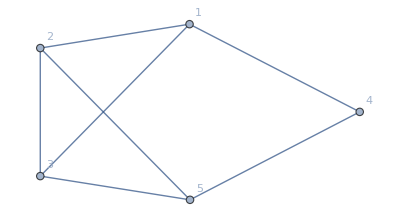

```mathematica
g = RandomGraph[{5,7}, VertexLabels->"Name"]
```

```mathematica
EdgeList[g]
```

{1<->2,1<->3,1<->4,2<->3,2<->5,3<->5,4<->5}

```mathematica
Export[FileNameJoin[{$HomeDirectory,"network-similarity/isomorphism_left.gml"}],Graph[{1,2,3,4,5},{1<->2,1<->3,1<->4,2<->3,2<->5,3<->5,4<->5},VertexSize->Large,VertexStyle->Red,GraphLayout->"SpringElectricalEmbedding"]
]
```

C:\Users\Marissa\network-similarity\isomorphism_left.gml

```mathematica
Export[FileNameJoin[{$HomeDirectory,"network-similarity/isomorphism_right.gml"}],Graph[{"a","b","c","d","e"},{"a"<->"b","a"<->"c","a"<->"d","b"<->"c","b"<->5,"c"<->"e","d"<->"e"},VertexSize->Large,VertexStyle->LightGray,GraphLayout->"StarEmbedding"]
]
```

C:\Users\Marissa\network-similarity\isomorphism_right.gml

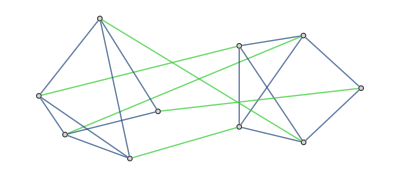

```mathematica
g = Import[FileNameJoin[{$HomeDirectory,"network-similarity/isomorphism_full.gml"}],VertexSize->Medium,VertexLabels->None,VertexLabelStyle->Medium]
```

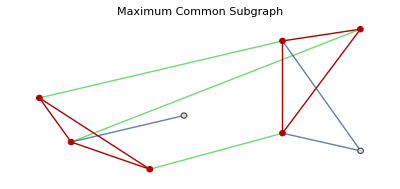

```mathematica
g3 = HighlightGraph[VertexDelete[g,{"e",4}],{"a","c","b",1,3,2,"a"<->"b","c"<->"b","a"<->"c",1<->2,2<->3,3<->1},
PlotLabel->Style[Framed[Style["Maximum Common Subgraph",16],FrameMargins->Large,FrameStyle->Directive[Black,Thickness[0.2]]],Black,FontFamily->"Helvetica"]]
```

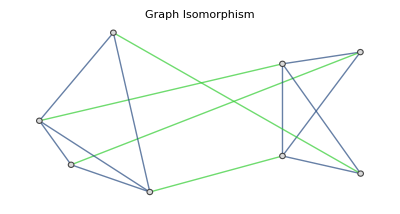

```mathematica
g1 = Import[FileNameJoin[{$HomeDirectory,"network-similarity/subgraph_isomorphism_full.gml"}],VertexSize->Medium,VertexLabels->None,VertexLabelStyle->Medium,
PlotLabel->Style[Framed[Style["Graph Isomorphism",16],FrameMargins->Large,FrameStyle->Directive[Black,Thickness[0.2]]],Black,FontFamily->"Helvetica"]]
```

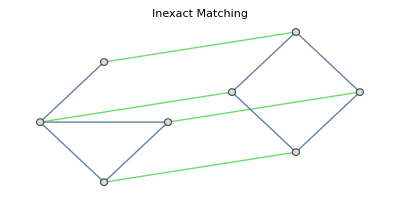

```mathematica
g4 = Import[FileNameJoin[{$HomeDirectory,"network-similarity/inexact_matching.gml"}],VertexSize->Medium,VertexLabels->None,VertexLabelStyle->Medium,PlotLabel->Style[Framed[Style["Inexact Matching",16],FrameMargins->Large,FrameStyle->Directive[Black,Thickness[0.2]]],Black,FontFamily->"Helvetica"]]
```

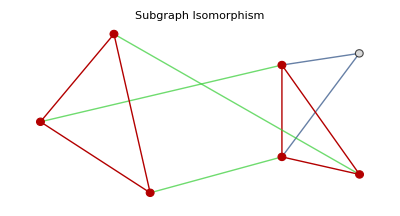

```mathematica
g2 = HighlightGraph[VertexDelete[g1,{"a"}],{2,3,5,"b","c","e",2<->3,2<->5,3<->5,"b"<->"c","c"<->"e","b"<->"e"},PlotLabel->Style[Framed[Style["Subgraph Isomorphism",16],FrameMargins->Large,FrameStyle->Directive[Black,Thickness[0.2]]],Black,FontFamily->"Helvetica"]]
```

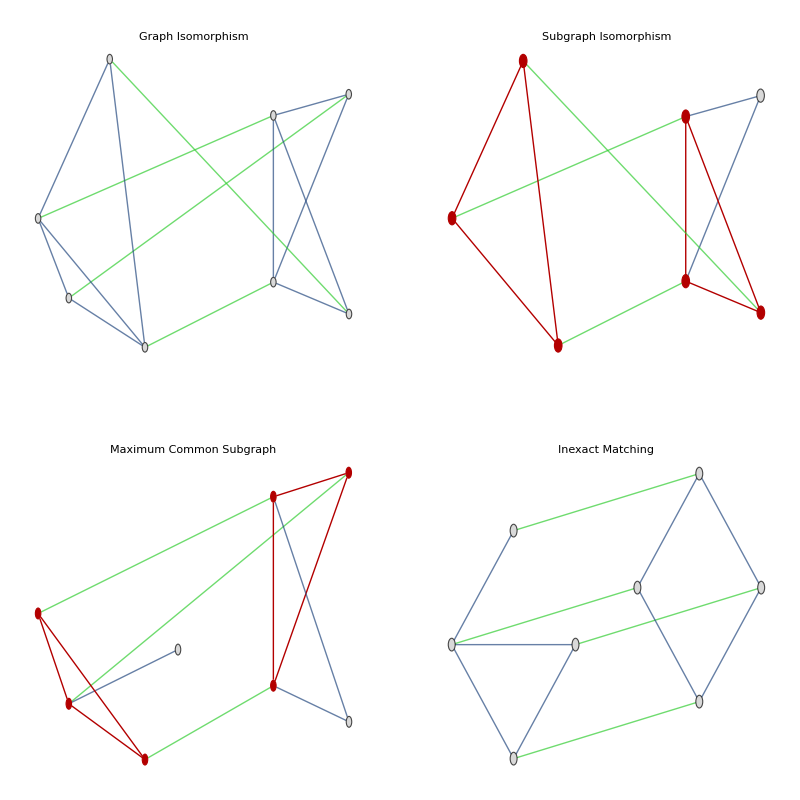

```mathematica
GraphicsGrid[{{g1,g2},{g3,g4}},Frame->All, ImageSize->Full]
```

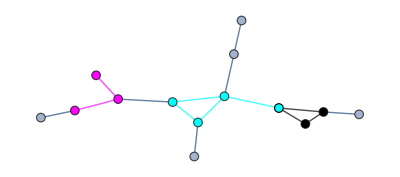

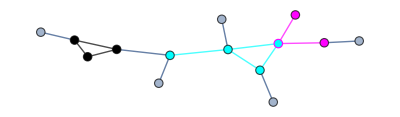

Last::nolast: {} has zero length and no last element.

ColorConvert::ccvinput: Last[{}] should be a valid image, a color directive, a list of machine-sized real numbers of length up to 5, or a list of such objects.

Last::nolast: {} has zero length and no last element.

ColorConvert::ccvinput: Last[{}] should be a valid image, a color directive, a list of machine-sized real numbers of length up to 5, or a list of such objects.

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

ColorConvert::ccvinput: Last[{}] should be a valid image, a color directive, a list of machine-sized real numbers of length up to 5, or a list of such objects.

General::stop: Further output of ColorConvert::ccvinput will be suppressed during this calculation.

C:\Users\Marissa\network-similarity\local_alignment_bottom.gml

Last::nolast: {} has zero length and no last element.

ColorConvert::ccvinput: Last[{}] should be a valid image, a color directive, a list of machine-sized real numbers of length up to 5, or a list of such objects.

Last::nolast: {} has zero length and no last element.

ColorConvert::ccvinput: Last[{}] should be a valid image, a color directive, a list of machine-sized real numbers of length up to 5, or a list of such objects.

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

ColorConvert::ccvinput: Last[{}] should be a valid image, a color directive, a list of machine-sized real numbers of length up to 5, or a list of such objects.

General::stop: Further output of ColorConvert::ccvinput will be suppressed during this calculation.

C:\Users\Marissa\network-similarity\local_alignment_top.gml

```mathematica
f1 = Graph[{1,2,3,4,5,6,7,8,9,"a1","a2","a3","a4","a5"},{1<->2,2<->3,1<->3,3<->4,4<->5,5<->6,6<->4,7<->8,8<->9,1<->"a1",4<->"a2","a2"<->"a3",5<->"a4",6<->8,9<->"a5"},VertexSize->Large,VertexStyle->{1->Black,2->Black,3->Directive[Cyan,EdgeForm[{Thick,Black}]],4->Cyan,5->Cyan,6->Cyan,7->Magenta,8->Magenta,9->Magenta},EdgeStyle->{1<->2->Black,2<->3->Black,1<->3->Black,3<->4->Cyan,4<->5->Cyan,4<->6->Cyan,5<->6->Cyan,7<->8->Magenta,8<->9->Magenta}]
f2 = Graph[{11,12,13,14,15,16,17,18,19,"b1","b2","b3","b4","b5"},{11<->12,12<->13,11<->13,13<->14,14<->15,15<->16,16<->17,17<->15,17<->19,17<->18,12<->"b1",14<->"b4",15<->"b2",16<->"b3",19<->"b5"},VertexSize->Large,
VertexStyle->{11->Black,12->Black,13->Black,14->Cyan,15->Cyan,16->Cyan,17->Directive[Cyan,EdgeForm[{Thick,Magenta}]],18->Magenta,19->Magenta},
EdgeStyle->{11<->12->Black,11<->13->Black,12<->13->Black,14<->15->Cyan,15<->16->Cyan,15<->17->Cyan,16<->17->Cyan,17<->18->Magenta,17<->19->Magenta}]
Export[FileNameJoin[{$HomeDirectory,"network-similarity/local_alignment_bottom.gml"}],f2]
Export[FileNameJoin[{$HomeDirectory,"network-similarity/local_alignment_top.gml"}],f1]
```

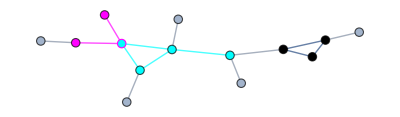

```mathematica
f2 = Import[FileNameJoin[{$HomeDirectory,"network-similarity/local_alignment_bottom.gml"}]]
```

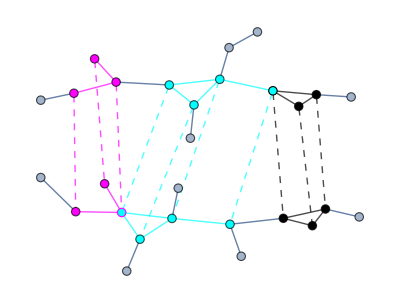

```mathematica
Show[Import[FileNameJoin[{$HomeDirectory,"network-similarity/local_alignment_temp.gml"}]]]
```

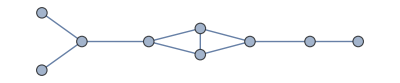

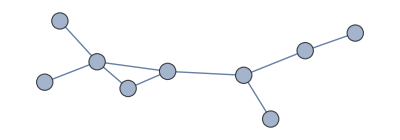

C:\Users\Marissa\network-similarity\global_alignment_bottom.gml

C:\Users\Marissa\network-similarity\global_alignment_top.gml

```mathematica
h1 = Graph[{1,2,3,4,5,6,7,8,9},{1<->2,2<->3,3<->4,3<->5,4<->5,4<->6,5<->6,6<->8,8<->7,8<->9},VertexSize->Large]
h2 = Graph[{11,12,14,15,16,17,18,19},{11<->13,12<->13,13<->15,13<->14,14<->15,14<->16,16<->17,16<->18,18<->19},VertexSize->Large]
Export[FileNameJoin[{$HomeDirectory,"network-similarity/global_alignment_bottom.gml"}],h2]
Export[FileNameJoin[{$HomeDirectory,"network-similarity/global_alignment_top.gml"}],h1]
```

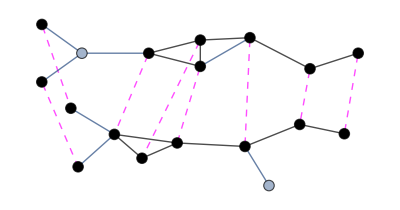

```mathematica
Show[Import[FileNameJoin[{$HomeDirectory,"network-similarity/global_alignment.gml"}]]]
```

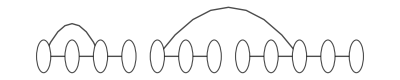

```mathematica
Show[Graph[{"a","b","c","d",1,2,3,4,5,6,7,8},{"a"<->"b","b"<->"c","c"<->"d","a"<->"c",1<->2,2<->3,4<->5,5<->6,6<->7,7<->8,1<->6},VertexCoordinates->Table[{i,0},{i,1,12}],VertexSize->0.5,VertexStyle->White,EdgeStyle->Black,VertexLabels->Placed["Name",Center],VertexLabelStyle->Medium,EdgeShapeFunction->{"a"<->"c"->GraphElementData[{"CurvedArc","Curvature"->1}],1<->6->GraphElementData[{"CurvedArc","Curvature"->0.6}]},ImageSize->Full]]
```

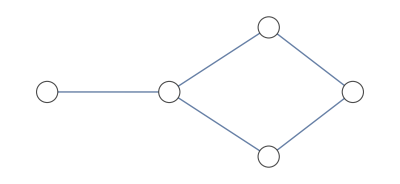

```mathematica
dPrime = Graph[{"a","b","c","d","e"},{"a"<->"b","a"<->"e","a"<->"d","b"<->"c","c"<->"d"},VertexLabels->Placed["Name",Center],VertexStyle->White,VertexSize->Medium,VertexLabelStyle->Medium]
```

```mathematica
dPrime1 =Graph[{1,2,3,4,5},{1<->2,1<->5,1<->4,2<->3,3<->4} ,VertexLabels->Placed["Name",Center],VertexStyle->White,VertexSize->Medium,VertexLabelStyle->Medium]
```

-Graphics-

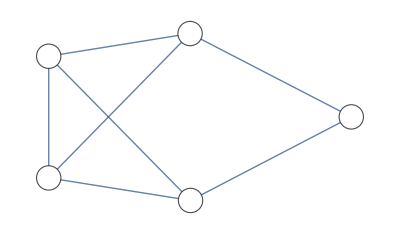

```mathematica
d1 = Graph[{1,2,3,4,5},{1<->2,1<->3,1<->4,2<->3,2<->5,3<->5,4<->5},VertexLabels->Placed["Name",Center],VertexStyle->White,VertexSize->Medium,VertexLabelStyle->Medium, GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
PropertyValue[{d1,5},VertexCoordinates]
```

{0.831804,0.}

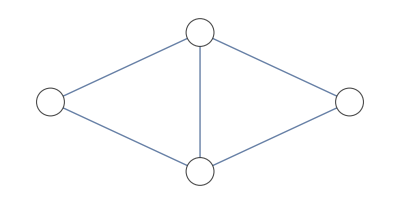

```mathematica
r1 = VertexDelete[d1,4]
```

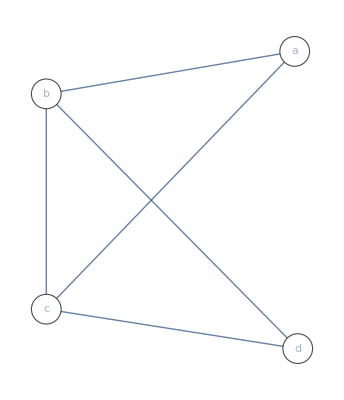

```mathematica
r2 = Graph[{"a","b","c","d","e"},{"a"<->"b","a"<->"c","a"<->"e","b"<->"c","b"<->"d","c"<->"d","d"<->"e"},VertexLabels->{"a"->Placed["a",Center],"b"->Placed["b",Center],"c"->Placed["c",Center],"e"->None,"d"->Placed["d",Center]},VertexStyle->{"a"->White,"b"->White,"c"->White,"e"->Directive[White,EdgeForm[None]],"d"->White},EdgeStyle->{"a"<->"e"->White,"d"<->"e"->White},
VertexCoordinates->{{0.82,0.98},{0,0.84},{0,0.13},{0.83,0},{0.82,0.49}},VertexSize->Medium,VertexLabelStyle->Medium]
```

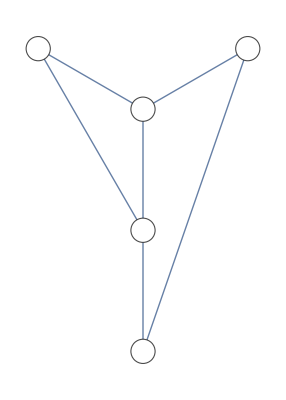

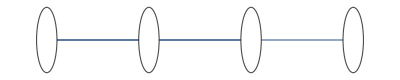

```mathematica
d2 =Graph[{1,2,3,4,5},{1<->2,1<->3,1<->5,2<->3,3<->4,4<->5},VertexLabels->Placed["Name",Center],VertexStyle->White,VertexSize->Medium,VertexLabelStyle->Medium, GraphLayout->"RadialEmbedding"]
```

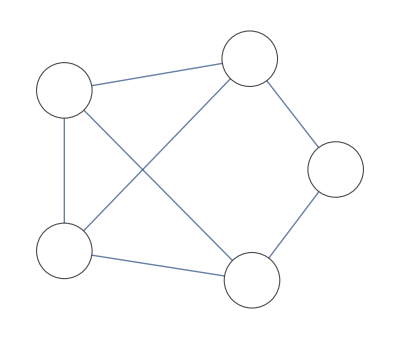

-Graphics-

```mathematica
Show[Graph[{1,2,3,4,5},{1<->2,1<->3,1<->4,2<->3,2<->5,3<->5,4<->5},VertexLabels->{2->Placed[1,Center]},VertexCoordinates->{{0.82,0.98},{0,0.84},{0,0.13},{1.2,0.49},{0.83,0}},VertexLabelStyle->Large,VertexSize->Large,VertexStyle->White]]
Show[Graph[{1,2,3,4,5},{1<->2,1<->3,1<->4,2<->3,2<->5,3<->5,4<->5},VertexLabels->{2->Placed["a",Center]},VertexCoordinates->{{0.82,0.98},{0,0.84},{0,0.13},{1.2,0.49},{0.83,0}},VertexLabelStyle->Large,VertexSize->Large,VertexStyle->White]]
```

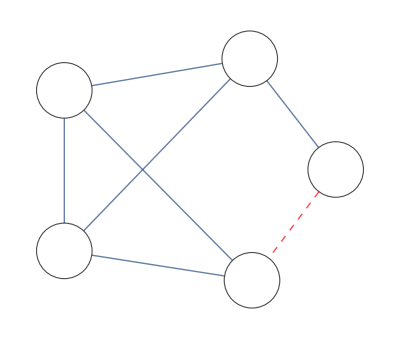

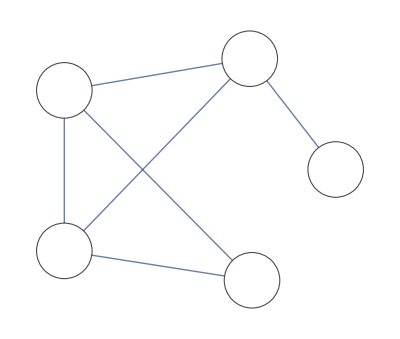

```mathematica
Show[Graph[{1,2,3,4,5},{1<->2,1<->3,1<->4,2<->3,2<->5,3<->5,4<->5},VertexCoordinates->{{0.82,0.98},{0,0.84},{0,0.13},{1.2,0.49},{0.83,0}},VertexLabelStyle->Medium,VertexSize->Large,VertexStyle->White,EdgeStyle->{4<->5->Directive[Thick,Red,Dashed]}]]
Show[Graph[{1,2,3,4,5},{1<->2,1<->3,1<->4,2<->3,2<->5,3<->5,4<->5},VertexCoordinates->{{0.82,0.98},{0,0.84},{0,0.13},{1.2,0.49},{0.83,0}},VertexLabelStyle->Medium,VertexSize->Large,VertexStyle->White,EdgeStyle->{4<->5->White}]]
```

-Graphics-

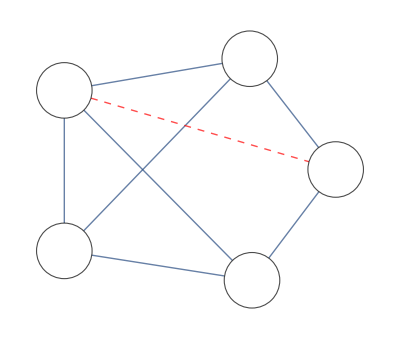

```mathematica
Show[Graph[{1,2,3,4,5},{1<->2,1<->3,1<->4,2<->3,2<->5,3<->5,4<->5},VertexCoordinates->{{0.82,0.98},{0,0.84},{0,0.13},{1.2,0.49},{0.83,0}},VertexLabelStyle->Medium,VertexSize->Large,VertexStyle->White]]
Show[Graph[{1,2,3,4,5},{1<->2,1<->3,1<->4,2<->3,2<->5,3<->5,4<->5,2<->4},VertexCoordinates->{{0.82,0.98},{0,0.84},{0,0.13},{1.2,0.49},{0.83,0}},VertexLabelStyle->Medium,VertexSize->Large,VertexStyle->White,EdgeStyle->{2<->4->Directive[Thick,Red,Dashed]}]]
```

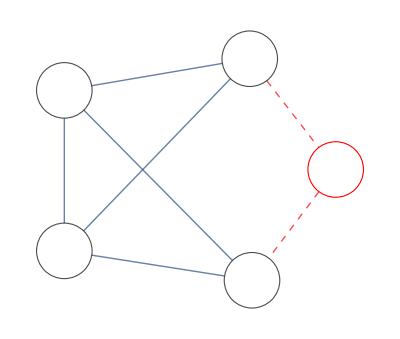

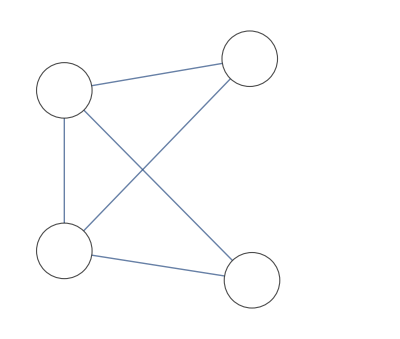

```mathematica
Show[Graph[{1,2,3,4,5},{1<->2,1<->3,1<->4,2<->3,2<->5,3<->5,4<->5},
VertexCoordinates->{{0.82,0.98},{0,0.84},{0,0.13},{1.2,0.49},{0.83,0}},VertexLabelStyle->Medium,VertexSize->Large,VertexStyle->{1->White,2->White,3->White,4->Directive[White,EdgeForm[{Red,Thick}]],5->White},EdgeStyle->{1<->4->Directive[Thick,Red,Dashed],4<->5->Directive[Thick,Red,Dashed]}]]
Show[Graph[{1,2,3,4,5},{1<->2,1<->3,1<->4,2<->3,2<->5,3<->5,4<->5},
VertexCoordinates->{{0.82,0.98},{0,0.84},{0,0.13},{1.2,0.49},{0.83,0}},VertexLabelStyle->Medium,VertexSize->Large,VertexStyle->{1->White,2->White,3->White,4->Directive[White,EdgeForm[None]],5->White},EdgeStyle->{1<->4->White,4<->5->White}]]
```

-Graphics-

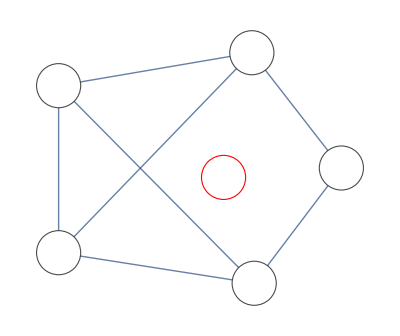

```mathematica
Show[Graph[{1,2,3,4,5},{1<->2,1<->3,1<->4,2<->3,2<->5,3<->5,4<->5},VertexCoordinates->{{0.82,0.98},{0,0.84},{0,0.13},{1.2,0.49},{0.83,0}},VertexLabelStyle->Medium,VertexSize->Large,VertexStyle->White]]
Show[Graph[{1,2,3,4,5,6},{1<->2,1<->3,1<->4,2<->3,2<->5,3<->5,4<->5},VertexCoordinates->{{0.82,0.98},{0,0.84},{0,0.13},{1.2,0.49},{0.83,0},{0.7,0.45}},VertexLabelStyle->Medium,VertexSize->Large,VertexStyle->{1->White,2->White,3->White,4->White,5->White,6->Directive[White,EdgeForm[{Red,Thick}]]}]]
```

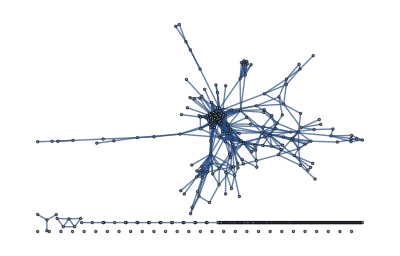

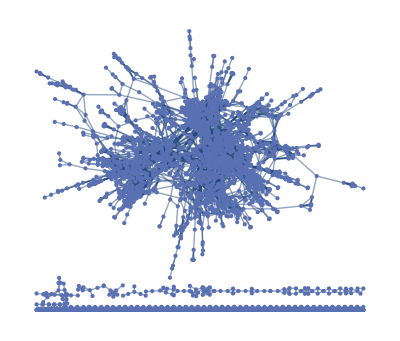

Vertex and edge counts of g95: 444, 1860

Vertex and edge counts of y95: 5100, 30118

```mathematica
AppendTo[$Path, FileNameJoin[{$HomeDirectory,"network-similarity"}]];
g95 = Import["mycoplasma_genitalium95.gml",ImageSize->Tiny]
y95 = Import["yeast95.gml",ImageSize->Tiny]
Print["Vertex and edge counts of g95: ", VertexCount[g95], ", ", EdgeCount[g95]];
Print["Vertex and edge counts of y95: ", VertexCount[y95], ", ", EdgeCount[y95]];
```

```mathematica
numStubs=VertexDegree[g95];
numverts = VertexCount[g95];
vertexlist=Range[numverts];
sortverts = Ordering[numStubs];
edgelist={};
For[i=1,i≤numverts,i++,
n=numStubs[[sortverts[[-i]]]];
If[n>0,
numStubs[[sortverts[[-i]]]]= 0;
neighbors = RandomSample[numStubs->vertexlist,n];
For[j=1,j≤n,j++,
numStubs[[neighbors[[j]]]]-=1;
AppendTo[edgelist,sortverts[[-i]]<->neighbors[[j]]];
];
];
]
g95rd = Graph[vertexlist,edgelist];
```

```mathematica
numStubs=VertexDegree[y95];
numverts=VertexCount[y95];
vertexlist=Range[numverts];
sortverts=Ordering[numStubs];
edgelist={};
For[i=1,i≤numverts,i++,n=numStubs[[sortverts[[-i]]]];
If[n>0,numStubs[[sortverts[[-i]]]]=0;
neighbors=RandomSample[numStubs->vertexlist,n];
For[j=1,j≤n,j++,numStubs[[neighbors[[j]]]]-=1;
AppendTo[edgelist,sortverts[[-i]]<->neighbors[[j]]];];];]
y95rd=Graph[vertexlist,edgelist];
```

```mathematica
g95r = RandomGraph[{VertexCount[g95],EdgeCount[g95]}];y95r = RandomGraph[{VertexCount[y95],EdgeCount[y95]}];
```

```mathematica
Max[VertexDegree[g95]]
Max[VertexDegree[g95r]]
Max[VertexDegree[g95rd]]
Max[VertexDegree[y95]]
Max[VertexDegree[y95r]]
Max[VertexDegree[y95rd]]
```

66

19

66

213

26

213

```mathematica
GlobalClusteringCoefficient[g95]//N
GlobalClusteringCoefficient[g95r]//N
GlobalClusteringCoefficient[g95rd]//N
GlobalClusteringCoefficient[y95]//N
GlobalClusteringCoefficient[y95r]//N
GlobalClusteringCoefficient[y95rd]//N
```

0.75828

0.0224913

0.41986

0.757033

0.00230494

0.149887

```mathematica
g95g2 =(LocalClusteringCoefficient[g95] *VertexDegree[g95]*(VertexDegree[g95]-1)/2);
g95rg2 =(LocalClusteringCoefficient[g95r]*VertexDegree[g95r]*(VertexDegree[g95r]-1)/2);
g95rdg2=(LocalClusteringCoefficient[g95rd]*VertexDegree[g95rd]*(VertexDegree[g95rd]-1)/2);
y95g2=(LocalClusteringCoefficient[y95]*VertexDegree[y95]*(VertexDegree[y95]-1)/2);
y95rg2=(LocalClusteringCoefficient[y95r]*VertexDegree[y95r]*(VertexDegree[y95r]-1)/2);
y95rdg2=(LocalClusteringCoefficient[y95rd]*VertexDegree[y95rd]*(VertexDegree[y95rd]-1)/2);
```

```mathematica
1860/444^2//N
30118/5100^2 //N
```

0.00943511

0.00115794

```mathematica
Max[y95g2]
Max[y95rg2]
Max[y95rdg2]
Max[g95g2]
Max[g95rg2]
Max[g95rdg2]
```

14592

3

3606

1376

6

774

```mathematica
Max[VertexDegree[g95r]]
```

17

```mathematica
HistogramList[y95rdg2,{0,Max[y95rdg2],50}]//N
```

{{0.,50.,100.,150.,200.,250.,300.,350.,400.,450.,500.,550.,600.,650.,700.,750.,800.,850.,900.,950.,1000.,1050.,1100.,1150.,1200.,1250.,1300.,1350.,1400.,1450.,1500.,1550.,1600.,1650.,1700.,1750.,1800.,1850.,1900.,1950.,2000.,2050.,2100.,2150.,2200.,2250.,2300.,2350.,2400.,2450.,2500.,2550.,2600.,2650.,2700.,2750.,2800.,2850.,2900.,2950.,3000.,3050.,3100.,3150.,3200.,3250.,3300.,3350.,3400.,3450.,3500.,3550.,3600.,3650.,3700.,3750.,3800.,3850.,3900.,3950.,4000.,4050.,4100.,4150.,4200.,4250.,4300.,4350.,4400.,4450.,4500.,4550.,4600.,4650.,4700.,4750.,4800.,4850.,4900.,4950.,5000.,5050.,5100.,5150.,5200.,5250.,5300.,5350.,5400.,5450.,5500.,5550.,5600.,5650.,5700.,5750.,5800.,5850.,5900.,5950.,6000.,6050.,6100.,6150.,6200.,6250.,6300.,6350.,6400.,6450.,6500.,6550.,6600.,6650.,6700.,6750.,6800.,6850.,6900.,6950.,7000.,7050.,7100.,7150.,7200.,7250.,7300.,7350.,7400.,7450.,7500.,7550.,7600.,7650.,7700.,7750.,7800.,7850.,7900.,7950.,8000.,8050.,8100.,8150.,8200.,8250.,8300.,8350.,8400.,8450.,8500.,8550.,8600.,8650.,8700.,8750.,8800.,8850.,8900.,8950.,9000.,9050.,9100.,9150.,9200.,9250.,9300.,9350.,9400.,9450.,9500.,9550.,9600.,9650.,9700.,9750.,9800.,9850.,9900.,9950.,10000.,10050.,10100.,10150.,10200.,10250.,10300.,10350.,10400.,10450.,10500.,10550.,10600.,10650.,10700.,10750.,10800.,10850.,10900.,10950.,11000.,11050.,11100.,11150.,11200.,11250.,11300.,11350.,11400.,11450.,11500.,11550.,11600.,11650.,11700.,11750.,11800.,11850.,11900.,11950.,12000.,12050.,12100.,12150.,12200.,12250.,12300.,12350.,12400.,12450.,12500.,12550.,12600.,12650.,12700.,12750.,12800.,12850.,12900.,12950.,13000.,13050.,13100.,13150.,13200.,13250.,13300.,13350.,13400.,13450.,13500.,13550.,13600.,13650.,13700.,13750.,13800.,13850.,13900.,13950.,14000.,14050.,14100.,14150.,14200.,14250.,14300.,14350.,14400.,14450.,14500.,14550.},{4335.,200.,87.,26.,21.,26.,14.,14.,17.,9.,14.,13.,20.,10.,4.,6.,1.,3.,3.,1.,0.,5.,1.,1.,2.,2.,1.,2.,2.,3.,2.,4.,0.,4.,3.,2.,1.,3.,4.,3.,2.,3.,1.,4.,3.,2.,0.,1.,3.,2.,5.,0.,3.,3.,1.,1.,4.,2.,3.,3.,2.,1.,1.,0.,2.,0.,2.,0.,1.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,1.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,2.,0.,0.,0.,1.,3.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,2.,1.,0.,0.,1.,0.,0.,0.,0.,1.,1.,0.,0.,0.,0.,1.,1.,0.,0.,1.,0.,1.,0.,0.,0.,0.,0.,3.,0.,0.,0.,0.,0.,1.,1.,0.,0.,0.,1.,1.,2.,2.,0.,0.,0.,1.,1.,1.,0.,1.,1.,0.,0.,0.,1.,1.,0.,1.,0.,1.,1.,3.,1.,2.,2.,3.,1.,0.,1.,1.,0.,1.,0.,1.,0.,1.,0.,1.,0.,1.,1.,1.,1.,0.,2.,1.,3.,5.,2.,2.,4.,1.,1.,0.,0.,2.,1.,1.,0.,1.,3.,1.,1.,0.,1.,1.,4.,2.,0.,3.,1.,0.,0.,0.,0.,0.,1.,3.,0.,2.,3.,1.,1.,1.,1.,3.,2.,1.,3.,1.,1.,1.,4.,4.,1.,4.,3.,0.,3.,4.,1.,4.,2.,1.,1.,2.,1.,1.,0.,2.,0.,1.,0.,0.}}

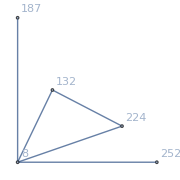

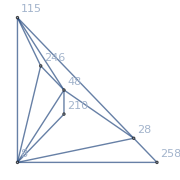

```mathematica
NeighborhoodGraph[g95,8,GraphLayout->"PlanarEmbedding",VertexLabels->"Name",ImageSize->Small]
NeighborhoodGraph[g95rd,8, GraphLayout->"PlanarEmbedding",VertexLabels->"Name",ImageSize->Small]
```

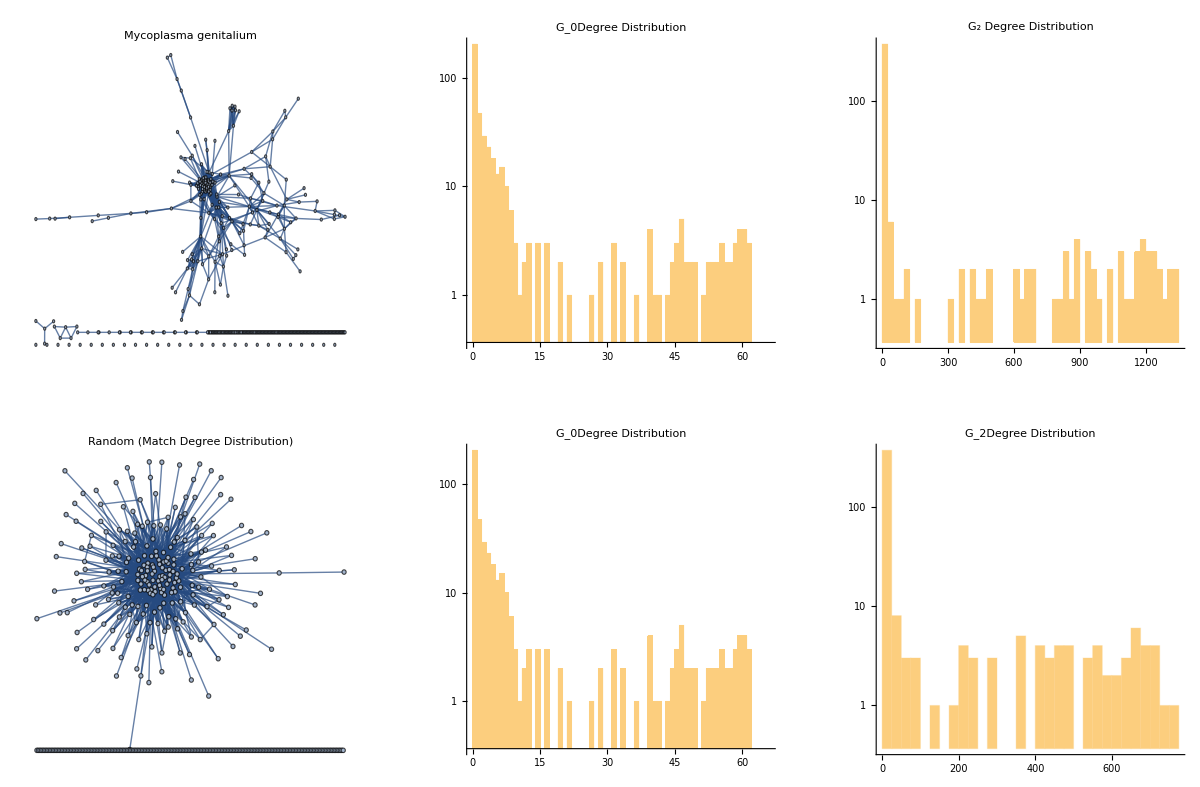

```mathematica
GraphicsGrid[{{Show[g95,GraphLayout->"SpringEmbedding",AspectRatio->1.0,PlotLabel->Style["Mycoplasma genitalium",Black,Large,Italic,FontFamily->"Helvetica"]],
Histogram[VertexDegree[g95],{0,Max[VertexDegree[g95]],1},ScalingFunctions->"Log",TicksStyle->Large,PlotLabel->Style["G_0Degree Distribution",Black,Large,FontFamily->"Helvetica"]],Histogram[g95g2,{0,Max[g95g2],25},PlotRange->{0,500},ScalingFunctions->"Log",TicksStyle->Large,PlotLabel->Style["G_2 Degree Distribution",Black,Large,FontFamily->"Helvetica"]]},
{Show[g95rd, PlotLabel->Style["Random (Match Degree Distribution)",Black,Large,FontFamily->"Helvetica"]],
Histogram[VertexDegree[g95rd],{0,Max[VertexDegree[g95]],1},ScalingFunctions->"Log",TicksStyle->Large,PlotLabel->Style["G_0Degree Distribution",Black,Large,FontFamily->"Helvetica"]],Histogram[g95rdg2,{0,Max[g95g2],25},PlotRange->{0,500},ScalingFunctions->"Log",TicksStyle->Large,PlotLabel->Style["G_2Degree Distribution",Black,Large,FontFamily->"Helvetica"]]}},Frame->None,ImageSize->Full]
```

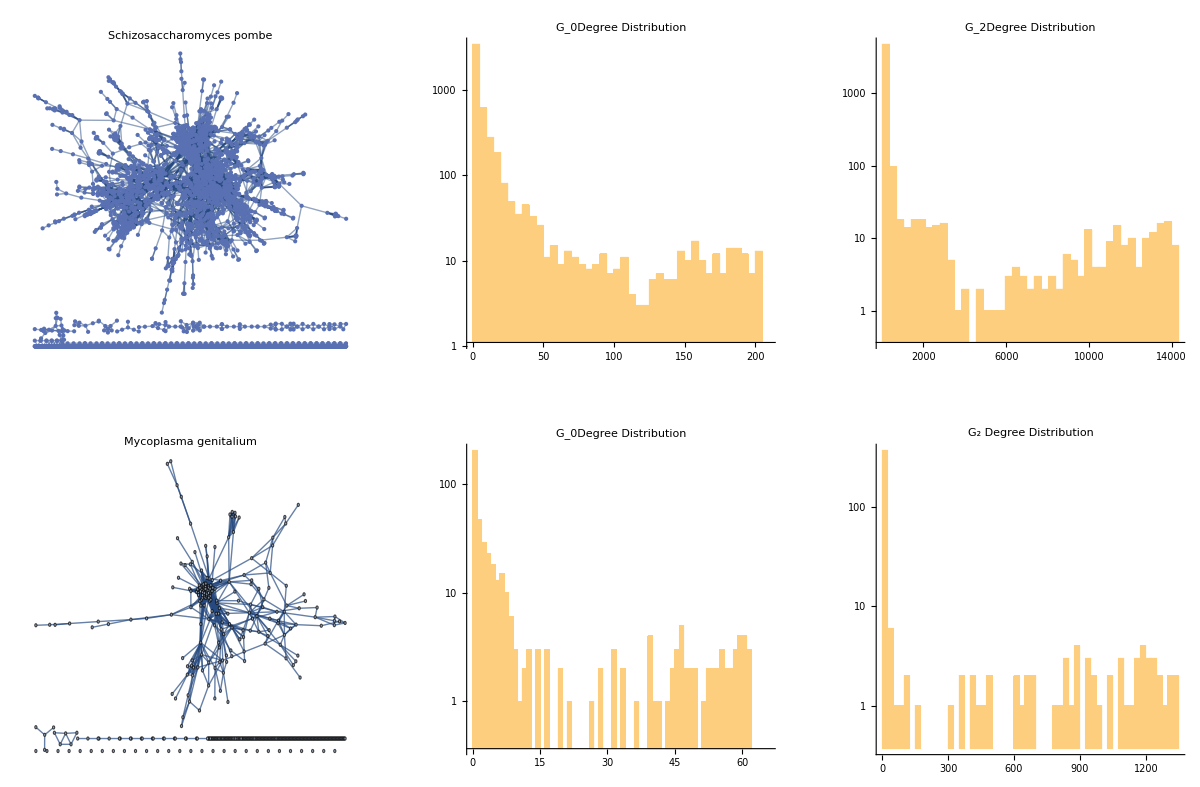

```mathematica
GraphicsGrid[{{Show[y95,GraphLayout->"SpringEmbedding",AspectRatio->1.0,VertexSize->Tiny,PlotLabel->Style["Schizosaccharomyces pombe",Black,Large,Italic,FontFamily->"Helvetica"]],Histogram[VertexDegree[y95],{0,Max[VertexDegree[y95]],5},ScalingFunctions->"Log",TicksStyle->Large,PlotLabel->Style["G_0Degree Distribution",Black,Large,FontFamily->"Helvetica"]],Histogram[y95g2,{0,Max[y95g2],350},ScalingFunctions->"Log",TicksStyle->Large,Ticks->{{2000,6000,10000,14000},Automatic},PlotLabel->Style["G_2Degree Distribution",Black,Large,FontFamily->"Helvetica"]]},{Show[g95,GraphLayout->"SpringEmbedding",AspectRatio->1.0,PlotLabel->Style["Mycoplasma genitalium",Black,Large,Italic,FontFamily->"Helvetica"]],
Histogram[VertexDegree[g95],{0,Max[VertexDegree[g95]],1},ScalingFunctions->"Log",TicksStyle->Large,PlotLabel->Style["G_0Degree Distribution",Black,Large,FontFamily->"Helvetica"]],Histogram[g95g2,{0,Max[g95g2],25},PlotRange->{0,500},ScalingFunctions->"Log",TicksStyle->Large,PlotLabel->Style["G_2 Degree Distribution",Black,Large,FontFamily->"Helvetica"]]},
{Show[g95rd, PlotLabel->Style["Random (Match Degree Distribution)",Black,Large,FontFamily->"Helvetica"]],
Histogram[VertexDegree[g95rd],{0,Max[VertexDegree[g95]],1},ScalingFunctions->"Log",TicksStyle->Large,PlotLabel->Style["G_0Degree Distribution",Black,Large,FontFamily->"Helvetica"]],Histogram[g95rdg2,{0,Max[g95g2],25},PlotRange->{0,500},ScalingFunctions->"Log",TicksStyle->Large,PlotLabel->Style["G_2Degree Distribution",Black,Large,FontFamily->"Helvetica"]]},
{Show[g95r, PlotLabel->Style["Random (Match Size and Edge Density)",Black,Large,FontFamily->"Helvetica"]],
Histogram[VertexDegree[g95r],{0,20,1},ScalingFunctions->"Log",TicksStyle->Large,PlotLabel->Style["G_0Degree Distribution",Black,Large,FontFamily->"Helvetica"]],Histogram[g95rg2,{0,50,1},PlotRange->{0,500},ScalingFunctions->"Log",TicksStyle->Large,PlotLabel->Style["G_2Degree Distribution",Black,Large,FontFamily->"Helvetica"]]}},Frame->None,ImageSize->Full]
```

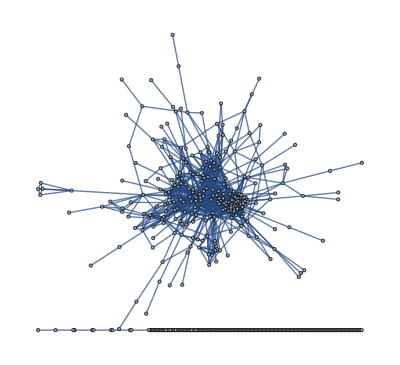

Vertex and edge counts of g90: 444, 2493

Vertex and edge counts of g90CC: 274, 2487

0.69256

0.258627

```mathematica
AppendTo[$Path, FileNameJoin[{$HomeDirectory,"network-similarity"}]];g90=Import["mycoplasma_genitalium90.gml"]
Print["Vertex and edge counts of g90: ",VertexCount[g90],", ",EdgeCount[g90]];
g90CC=Subgraph[g90,ConnectedComponents[g90][[1]]];
Print["Vertex and edge counts of g90CC: ",VertexCount[g90CC],", ",EdgeCount[g90CC]];
outStubs=VertexDegree[g90];
inStubs=VertexDegree[g90];
vertexlist=Range[VertexCount[g90]];
edgelist={};
For[i=1,i≤EdgeCount[g90],i++,source=RandomSample[outStubs->vertexlist,1][[1]];
target=RandomSample[inStubs->vertexlist,1][[1]];
outStubs[[source]]-=1;
inStubs[[target]]-=1;
AppendTo[edgelist,source<->target];]
degMimic90=Graph[vertexlist,edgelist,ImageSize->Full];

GlobalClusteringCoefficient[g90]//N
GlobalClusteringCoefficient[degMimic90]//N
```

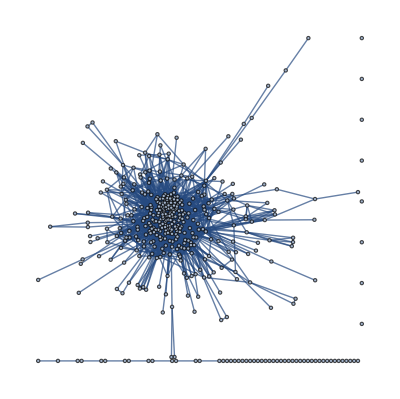

Vertex and edge counts of g70: 444, 5326

Vertex and edge counts of g70CC: 385, 5318

0.553878

0.242991

```mathematica
AppendTo[$Path, FileNameJoin[{$HomeDirectory,"network-similarity"}]];
g70=Import["mycoplasma_genitalium70.gml"]
Print["Vertex and edge counts of g70: ",VertexCount[g70],", ",EdgeCount[g70]];
g70CC=Subgraph[g70,ConnectedComponents[g70][[1]]];
Print["Vertex and edge counts of g70CC: ",VertexCount[g70CC],", ",EdgeCount[g70CC]];
outStubs=VertexDegree[g70];
inStubs=VertexDegree[g70];
vertexlist=Range[VertexCount[g70]];
edgelist={};
For[i=1,i≤EdgeCount[g70],i++,
source=RandomSample[outStubs->vertexlist,1][[1]];
target=RandomSample[inStubs->vertexlist,1][[1]];
outStubs[[source]]-=1;
inStubs[[target]]-=1;
AppendTo[edgelist,source<->target];]
degMimic70=Graph[vertexlist,edgelist,ImageSize->Full];

GlobalClusteringCoefficient[g70]//N
GlobalClusteringCoefficient[degMimic70]//N
```

{exact,inexact,approximate/
suboptimal,motifs/
graphlets,local 
alignment,global 
alignment}

{exact→Placed[exact,Center],inexact→Placed[inexact,Center],approximate/
suboptimal→Placed[approximate/
suboptimal,Center],motifs/
graphlets→Placed[motifs/
graphlets,Center],local 
alignment→Placed[local 
alignment,Center],global 
alignment→Placed[global 
alignment,Center]}

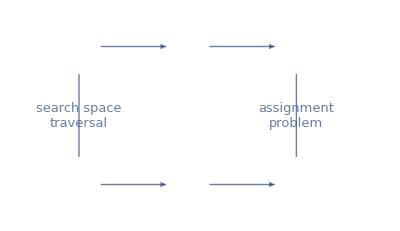

```mathematica
edges = {"exact"->"inexact", "inexact"->"approximate/\nsuboptimal", "exact"<->"motifs/\ngraphlets","motifs/\ngraphlets"->"local \nalignment","local \nalignment"->"global \nalignment","global \nalignment"<->"approximate/\nsuboptimal"};
g = Graph[edges];
vertices = VertexList[g]
labels = Table[vertices[[i]]->Placed[Pane[Style[vertices[[i]],LineSpacing->{1,0}],250,FrameMargins->None,ImageSize->Small,ImageSizeAction->"ShrinkToFit"],Center],{i,1,Length[vertices]}]
Show[Graph[edges, VertexLabels->labels,VertexSize->Large, VertexShapeFunction->"ConcaveSquare", VertexStyle->Directive[Transparent,EdgeForm[None]],VertexLabelStyle->16,EdgeLabelStyle->13,GraphLayout->{"GridEmbedding","Dimension"->{2,3}},VertexCoordinates->{{0,2},{2,2},{4,2},{0,0},{2,0},{4,0}},
EdgeLabels->{"exact"<->"motifs/\ngraphlets"->"search space\ntraversal","global \nalignment"<->"approximate/\nsuboptimal"->"assignment\nproblem"},ImageSize->Full]]
```